```mathematica
If[$MachineName=="Cirrus",
PacletDirectoryAdd["/Volumes/klaus/github/EcoEvo"],
PacletDirectoryAdd["~/github/EcoEvo"]
];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.0X (July 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

## Models

### juvenile-adult

```mathematica
ja={
Guild[n]->{Components->{j,a},Traits->{x}},
Transitions:>{
{{Subscript[j, i]⇒Subscript[a, i]},m[Subscript[x[j], i]] Subscript[j, i]},
{{0 Subscript[a, i]⇒Subscript[j, i]},b Subscript[a, i],NormalDistribution[0,σμ]},
{{Subscript[j, i]⇒∅},dj[Subscript[x[j], i]] Subscript[j, i]},
{{Subscript[a, i]⇒∅},da[Subscript[x[a], i]] Subscript[a, i]}
}
};
```

### two-patch

```mathematica
tp={
Guild[n]->{
Components->{n1,n2},
Traits->{x}
},
Transitions:>{
{{Subscript[n1, i]⇒∅},d1[Subscript[x[n1], i]] Subscript[n1, i]+d0 Sum[Subscript[n1, j],{j,Subscript[𝒩, n]}] Subscript[n1, i]},
{{Subscript[n2, i]⇒∅},d2[Subscript[x[n2], i]] Subscript[n2, i]+d0 Sum[Subscript[n2, j],{j,Subscript[𝒩, n]}] Subscript[n2, i]},
{{0 Subscript[n1, i]⇒Subscript[n1, i]},b Subscript[n1, i],NormalDistribution[0,σμ]},
{{0 Subscript[n2, i]⇒Subscript[n2, i]},b Subscript[n2, i],NormalDistribution[0,σμ]},
{{Subscript[n1, i]⇒Subscript[n2, i]},d12 Subscript[n1, i]},
{{Subscript[n2, i]⇒Subscript[n1, i]},d21 Subscript[n2, i]}
},
Parameters:>{b>=0,d0>=0,d12>=0,d21>=0,σμ>=0}
};
```

## Private Parts

### tp

```mathematica
SetModel[tp];
```

```mathematica
EcoEvo`Private`dndt[n1]
EcoEvo`Private`dndt[n2]
EcoEvo`Private`dxdt[n1]
EcoEvo`Private`dxdt[n2]
EcoEvo`Private`dGdt[n1]
EcoEvo`Private`dGdt[n2]
```

(b+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) n1_i+(-d12+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) n1_i+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG] n1_i+(d21+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) n2_i+n1_i (-d1[x[n1]_i]+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]-d0 ∑_j^𝒩[n] n1_j)

(d12+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) n1_i+(b+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) n2_i+(-d21+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) n2_i+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG] n2_i+n2_i (-d2[x[n2]_i]+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]-d0 ∑_j^𝒩[n] n2_j)

{4 EcoEvo`Private`sourceG.{0}+1/n1_i n2_i (EcoEvo`Private`sourceG.{0}+(d21+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) (-x_i[n1]+x_i[n2]))}

{4 EcoEvo`Private`sourceG.{0}+1/n2_i n1_i (EcoEvo`Private`sourceG.{0}+(d12+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) (x_i[n1]-x_i[n2]))}

{{{0}.Transpose[EcoEvo`Private`sourceG.{0}]+4 EcoEvo`Private`sourceG.{{0}}.EcoEvo`Private`sourceG+(b+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) (EcoEvo`Private`sourceG+σμ^2-(Var[x][n1])_i)+1/n1_i n2_i ({-x_i[n1]+x_i[n2]}.Transpose[EcoEvo`Private`sourceG.{0}]+EcoEvo`Private`sourceG.{{0}}.EcoEvo`Private`sourceG+(d21+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) (EcoEvo`Private`sourceG-(Var[x][n1])_i+(-x_i[n1]+x_i[n2])^2))}}

{{{0}.Transpose[EcoEvo`Private`sourceG.{0}]+4 EcoEvo`Private`sourceG.{{0}}.EcoEvo`Private`sourceG+(b+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) (EcoEvo`Private`sourceG+σμ^2-(Var[x][n2])_i)+1/n2_i n1_i ({x_i[n1]-x_i[n2]}.Transpose[EcoEvo`Private`sourceG.{0}]+EcoEvo`Private`sourceG.{{0}}.EcoEvo`Private`sourceG+(d12+1/2 DoubleDotProduct[{{0}},EcoEvo`Private`sourceG]) (EcoEvo`Private`sourceG-(Var[x][n2])_i+(x_i[n1]-x_i[n2])^2))}}

### ja

```mathematica
SetModel[ja];
```

```mathematica
EcoEvo`Private`dndt[j]
EcoEvo`Private`dndt[a]
EcoEvo`Private`dxdt[j]
EcoEvo`Private`dxdt[a]
EcoEvo`Private`dGdt[j]
EcoEvo`Private`dGdt[a]
```

b a_i+j_i (-dj[x[j]_i]-1/2 (Var[x][j])_i dj''[x[j]_i])+j_i (-m[x[j]_i]-1/2 (Var[x][j])_i m''[x[j]_i])

m[x[j]_i] j_i+a_i (-da[x[a]_i]-1/2 (Var[x][a])_i da''[x[a]_i])

{(b a_i (x[a]_i-x[j]_i))/j_i+(Var[x][j])_i (-dj'[x[j]_i]-1/2 (Var[x][j])_i dj^(3)[x[j]_i])+(Var[x][j])_i (-m'[x[j]_i]-1/2 (Var[x][j])_i m^(3)[x[j]_i])}

{(Var[x][a])_i (-da'[x[a]_i]-1/2 (Var[x][a])_i da^(3)[x[a]_i])+1/a_i j_i ((-x[a]_i+x[j]_i) (m[x[j]_i]+1/2 (Var[x][j])_i m''[x[j]_i])+(Var[x][j])_i (m'[x[j]_i]+1/2 (Var[x][j])_i m^(3)[x[j]_i]))}

{{(b a_i (σμ^2+(x[a]_i-x[j]_i)^2+(Var[x][a])_i-(Var[x][j])_i))/j_i-(Var[x][j])_i^2 dj''[x[j]_i]-(Var[x][j])_i^2 m''[x[j]_i]}}

{{-(Var[x][a])_i^2 da''[x[a]_i]+1/a_i j_i ((Var[x][j])_i^2 m''[x[j]_i]+((-x[a]_i+x[j]_i)^2-(Var[x][a])_i+(Var[x][j])_i) (m[x[j]_i]+1/2 (Var[x][j])_i m''[x[j]_i])+2 (-x[a]_i+x[j]_i) (Var[x][j])_i (m'[x[j]_i]+1/2 (Var[x][j])_i m^(3)[x[j]_i]))}}

## DoubleDotProduct

```mathematica
DoubleDotProduct[{{a11,a12},{a21,a22}},{{b11,b12},{b21,b22}}]
```

a11 b11+a12 b12+a21 b21+a22 b22

## MakeGMatrix

```mathematica
?MakeGMatrix
```

```mathematica
SetModel[tp]
```

```mathematica
MakeGMatrix[n]
```

{{Var[x]}}

## AttributesAndGsQ / AttributesVariablesAndGsQ

### tp

```mathematica
SetModel[tp]
```

```mathematica
AttributesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0}]]
```

False

```mathematica
AttributesVariablesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0}]]
```

True

```mathematica
AttributesVariablesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1}]]
```

False

```mathematica
AttributesVariablesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0}]]
```

False

## ExtractVarCovs

### tp

```mathematica
SetModel[tp]
```

```mathematica
ExtractVarCovs[{
Subscript[Var[x][n1], 1]->1,
Var[x][n1]->1,
Subscript[Var[x], 1]->1,
Var[x]->1,
Cov[x,x]->10,
Subscript[x, 1]->10
}]
```

{(Var[x][n1])_1→1,Var[x][n1]→1,Var[x]_1→1,Var[x]→1,Cov[x,x]→10}

## *Eqns

### tp

```mathematica
SetModel[tp]
```

```mathematica
Clear[d1,d2];
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]//TableForm
TraitEqns[{Subscript[𝒩, n]->1}]//TableForm
VarEqns[{Subscript[𝒩, n]->1}]//TableForm
```

n1_1'[t]==b n1_1[t]-d12 n1_1[t]+d21 n2_1[t]+n1_1[t] (-d1[x[n1]_1[t]]-d0 n1_1[t]-1/2 (Var[x][n1])_1[t] d1''[x[n1]_1[t]])
n2_1'[t]==d12 n1_1[t]+b n2_1[t]-d21 n2_1[t]+n2_1[t] (-d2[x[n2]_1[t]]-d0 n2_1[t]-1/2 (Var[x][n2])_1[t] d2''[x[n2]_1[t]])

x[n1]_1'[t]==(d21 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]+(Var[x][n1])_1[t] (-d1'[x[n1]_1[t]]-1/2 (Var[x][n1])_1[t] d1^(3)[x[n1]_1[t]])
x[n2]_1'[t]==(d12 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]+(Var[x][n2])_1[t] (-d2'[x[n2]_1[t]]-1/2 (Var[x][n2])_1[t] d2^(3)[x[n2]_1[t]])

(Var[x][n1])_1'[t]==b σμ^2+(d21 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t]-((Var[x][n1])_1[t])^2 d1''[x[n1]_1[t]]
(Var[x][n2])_1'[t]==b σμ^2+(d12 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-((Var[x][n2])_1[t])^2 d2''[x[n2]_1[t]]

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]//TableForm
TraitEqns[{Subscript[𝒩, n]->2}]//TableForm
VarEqns[{Subscript[𝒩, n]->2}]//TableForm
```

n1_1'[t]==b n1_1[t]-d12 n1_1[t]+d21 n2_1[t]+n1_1[t] (-d1[x[n1]_1[t]]-d0 (n1_1[t]+n1_2[t])-1/2 (Var[x][n1])_1[t] d1''[x[n1]_1[t]])
n2_1'[t]==d12 n1_1[t]+b n2_1[t]-d21 n2_1[t]+n2_1[t] (-d2[x[n2]_1[t]]-d0 (n2_1[t]+n2_2[t])-1/2 (Var[x][n2])_1[t] d2''[x[n2]_1[t]])
n1_2'[t]==b n1_2[t]-d12 n1_2[t]+d21 n2_2[t]+n1_2[t] (-d1[x[n1]_2[t]]-d0 (n1_1[t]+n1_2[t])-1/2 (Var[x][n1])_2[t] d1''[x[n1]_2[t]])
n2_2'[t]==d12 n1_2[t]+b n2_2[t]-d21 n2_2[t]+n2_2[t] (-d2[x[n2]_2[t]]-d0 (n2_1[t]+n2_2[t])-1/2 (Var[x][n2])_2[t] d2''[x[n2]_2[t]])

x[n1]_1'[t]==(d21 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]+(Var[x][n1])_1[t] (-d1'[x[n1]_1[t]]-1/2 (Var[x][n1])_1[t] d1^(3)[x[n1]_1[t]])
x[n2]_1'[t]==(d12 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]+(Var[x][n2])_1[t] (-d2'[x[n2]_1[t]]-1/2 (Var[x][n2])_1[t] d2^(3)[x[n2]_1[t]])
x[n1]_2'[t]==(d21 n2_2[t] (-x[n1]_2[t]+x[n2]_2[t]))/n1_2[t]+(Var[x][n1])_2[t] (-d1'[x[n1]_2[t]]-1/2 (Var[x][n1])_2[t] d1^(3)[x[n1]_2[t]])
x[n2]_2'[t]==(d12 n1_2[t] (x[n1]_2[t]-x[n2]_2[t]))/n2_2[t]+(Var[x][n2])_2[t] (-d2'[x[n2]_2[t]]-1/2 (Var[x][n2])_2[t] d2^(3)[x[n2]_2[t]])

(Var[x][n1])_1'[t]==b σμ^2+(d21 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t]-((Var[x][n1])_1[t])^2 d1''[x[n1]_1[t]]
(Var[x][n2])_1'[t]==b σμ^2+(d12 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-((Var[x][n2])_1[t])^2 d2''[x[n2]_1[t]]
(Var[x][n1])_2'[t]==b σμ^2+(d21 n2_2[t] ((-x[n1]_2[t]+x[n2]_2[t])^2-(Var[x][n1])_2[t]+(Var[x][n2])_2[t]))/n1_2[t]-((Var[x][n1])_2[t])^2 d1''[x[n1]_2[t]]
(Var[x][n2])_2'[t]==b σμ^2+(d12 n1_2[t] ((x[n1]_2[t]-x[n2]_2[t])^2+(Var[x][n1])_2[t]-(Var[x][n2])_2[t]))/n2_2[t]-((Var[x][n2])_2[t])^2 d2''[x[n2]_2[t]]

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
σμ=0.1;
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]//TableForm
TraitEqns[{Subscript[𝒩, n]->1}]//TableForm
VarEqns[{Subscript[𝒩, n]->1}]//TableForm
```

n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-0.1 n1_1[t]-(1+x[n1]_1[t])^2-(Var[x][n1])_1[t])
n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-0.1 n2_1[t]-(-1+x[n2]_1[t])^2-(Var[x][n2])_1[t])

x[n1]_1'[t]==(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]-2 (1+x[n1]_1[t]) (Var[x][n1])_1[t]
x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]-2 (-1+x[n2]_1[t]) (Var[x][n2])_1[t]

(Var[x][n1])_1'[t]==0.01-2 ((Var[x][n1])_1[t])^2+(0.01 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t]
(Var[x][n2])_1'[t]==0.01+(0.01 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-2 ((Var[x][n2])_1[t])^2

```mathematica
EcoEqns[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2}]//TableForm
```

n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-0.49-0.1 n1_1[t]-(Var[x][n1])_1[t])
n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-0.64-0.1 n2_1[t]-(Var[x][n2])_1[t])

```mathematica
EcoEqns[{Subscript[x, 1]->-0.3}]//TableForm
```

n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-0.49-0.1 n1_1[t]-(Var[x][n1])_1[t])
n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1.69-0.1 n2_1[t]-(Var[x][n2])_1[t])

```mathematica
TraitEqns[{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},{Subscript[Var[x][n1], 1]->0.24,Subscript[Var[x][n2], 1]->0.66}]//TableForm
```

x[n1]_1'[t]==-0.48 (1+x[n1]_1[t])+(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]
x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]-1.32 (-1+x[n2]_1[t])

### ja

```mathematica
SetModel[ja]
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]
```

{j_1'[t]==b a_1[t]-dj[x[j]_1[t]] j_1[t]-m[x[j]_1[t]] j_1[t],a_1'[t]==-da[x[a]_1[t]] a_1[t]+m[x[j]_1[t]] j_1[t]}

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]
```

{j_1'[t]==b a_1[t]-dj[x[j]_1[t]] j_1[t]-m[x[j]_1[t]] j_1[t],a_1'[t]==-da[x[a]_1[t]] a_1[t]+m[x[j]_1[t]] j_1[t],j_2'[t]==b a_2[t]-dj[x[j]_2[t]] j_2[t]-m[x[j]_2[t]] j_2[t],a_2'[t]==-da[x[a]_2[t]] a_2[t]+m[x[j]_2[t]] j_2[t]}

```mathematica
TraitEqns[{Subscript[𝒩, n]->1}]
```

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-(Var[x][j])_1[t] dj'[x[j]_1[t]]-(Var[x][j])_1[t] m'[x[j]_1[t]],x[a]_1'[t]==-(Var[x][a])_1[t] da'[x[a]_1[t]]+(j_1[t] (m[x[j]_1[t]] (-x[a]_1[t]+x[j]_1[t])+(Var[x][j])_1[t] m'[x[j]_1[t]]))/a_1[t]}

```mathematica
TraitEqns[{Subscript[𝒩, n]->2}]
```

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-(Var[x][j])_1[t] dj'[x[j]_1[t]]-(Var[x][j])_1[t] m'[x[j]_1[t]],x[a]_1'[t]==-(Var[x][a])_1[t] da'[x[a]_1[t]]+(j_1[t] (m[x[j]_1[t]] (-x[a]_1[t]+x[j]_1[t])+(Var[x][j])_1[t] m'[x[j]_1[t]]))/a_1[t],x[j]_2'[t]==(b a_2[t] (x[a]_2[t]-x[j]_2[t]))/j_2[t]-(Var[x][j])_2[t] dj'[x[j]_2[t]]-(Var[x][j])_2[t] m'[x[j]_2[t]],x[a]_2'[t]==-(Var[x][a])_2[t] da'[x[a]_2[t]]+(j_2[t] (m[x[j]_2[t]] (-x[a]_2[t]+x[j]_2[t])+(Var[x][j])_2[t] m'[x[j]_2[t]]))/a_2[t]}

```mathematica
TraitEqns[{Subscript[𝒩, n]->1},{Subscript[Var[x][j], 1]->1,Subscript[Var[x][a], 1]->1}]
```

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-dj'[x[j]_1[t]]-m'[x[j]_1[t]],x[a]_1'[t]==-da'[x[a]_1[t]]+(j_1[t] (m[x[j]_1[t]] (-x[a]_1[t]+x[j]_1[t])+m'[x[j]_1[t]]))/a_1[t]}

```mathematica
VarEqns[{Subscript[𝒩, n]->1}]
```

{(Var[x][j])_1'[t]==(b a_1[t] ((x[a]_1[t]-x[j]_1[t])^2+(Var[x][a])_1[t]-(Var[x][j])_1[t]))/j_1[t]-((Var[x][j])_1[t])^2 dj''[x[j]_1[t]]-((Var[x][j])_1[t])^2 m''[x[j]_1[t]],(Var[x][a])_1'[t]==-((Var[x][a])_1[t])^2 da''[x[a]_1[t]]+1/a_1[t]j_1[t] (m[x[j]_1[t]] ((-x[a]_1[t]+x[j]_1[t])^2-(Var[x][a])_1[t]+(Var[x][j])_1[t])+2 (-x[a]_1[t]+x[j]_1[t]) (Var[x][j])_1[t] m'[x[j]_1[t]]+((Var[x][j])_1[t])^2 m''[x[j]_1[t]])}

```mathematica
VarEqns[{Subscript[𝒩, n]->2}]
```

{(Var[x][j])_1'[t]==(b a_1[t] ((x[a]_1[t]-x[j]_1[t])^2+(Var[x][a])_1[t]-(Var[x][j])_1[t]))/j_1[t]-((Var[x][j])_1[t])^2 dj''[x[j]_1[t]]-((Var[x][j])_1[t])^2 m''[x[j]_1[t]],(Var[x][a])_1'[t]==-((Var[x][a])_1[t])^2 da''[x[a]_1[t]]+1/a_1[t]j_1[t] (m[x[j]_1[t]] ((-x[a]_1[t]+x[j]_1[t])^2-(Var[x][a])_1[t]+(Var[x][j])_1[t])+2 (-x[a]_1[t]+x[j]_1[t]) (Var[x][j])_1[t] m'[x[j]_1[t]]+((Var[x][j])_1[t])^2 m''[x[j]_1[t]]),(Var[x][j])_2'[t]==(b a_2[t] ((x[a]_2[t]-x[j]_2[t])^2+(Var[x][a])_2[t]-(Var[x][j])_2[t]))/j_2[t]-((Var[x][j])_2[t])^2 dj''[x[j]_2[t]]-((Var[x][j])_2[t])^2 m''[x[j]_2[t]],(Var[x][a])_2'[t]==-((Var[x][a])_2[t])^2 da''[x[a]_2[t]]+1/a_2[t]j_2[t] (m[x[j]_2[t]] ((-x[a]_2[t]+x[j]_2[t])^2-(Var[x][a])_2[t]+(Var[x][j])_2[t])+2 (-x[a]_2[t]+x[j]_2[t]) (Var[x][j])_2[t] m'[x[j]_2[t]]+((Var[x][j])_2[t])^2 m''[x[j]_2[t]])}

## EcoSim

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

sol=NDSolve[{n1_1'[t]==0.99 n1_1[t]+(-0.49-0.1 n1_1[t]) n1_1[t]+0.01 n2_1[t],n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+(-1.69-0.1 n2_1[t]) n2_1[t],n1_1[0]==0.1,n2_1[0]==0.1},{n1_1,n2_1},{t,0,100}]⟦1⟧

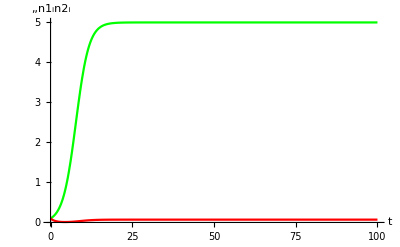

{n1_1→5.00141,n2_1→0.070734}

```mathematica
sol=EcoSim[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->-0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},100,Verbose->True];
PlotDynamics[sol]
FinalSlice[sol]
```

```mathematica
(* no-comp trait *)
sol=EcoSim[{Subscript[x, 1]->-0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},100];
FinalSlice[sol]
```

{n1_1→5.00141,n2_1→0.070734}

```mathematica
(* non-zero Var's *)
sol=EcoSim[{Subscript[x, 1]->-0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Var[x]->0.1},100];
FinalSlice[sol]
```

{n1_1→4.00124,n2_1→0.0497067}

```mathematica
(* non-zero Var's *)
sol=EcoSim[{Subscript[x, 1]->-0.3,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Var[x]->0.1},100];
FinalSlice[sol]
```

{n1_1→4.00124,n2_1→0.0497067}

```mathematica
(* TODO: no popic comps *)
sol=EcoSim[{Subscript[x, 1]->-0.3},{Subscript[n, 1]->0.1},100];
FinalSlice[sol]
```

FinalSlice[EcoSim[{x_1→-0.3},{n_1→0.1},100]]

sol=NDSolve[{n1_1'[t]==0.99 n1_1[t]+n1_1[t] (-0.49-0.1 (n1_1[t]+n1_2[t]))+0.01 n2_1[t],n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1.44-0.1 (n2_1[t]+n2_2[t])),n1_2'[t]==0.99 n1_2[t]+n1_2[t] (-1.69-0.1 (n1_1[t]+n1_2[t]))+0.01 n2_2[t],n2_2'[t]==0.01 n1_2[t]+0.99 n2_2[t]+n2_2[t] (-0.64-0.1 (n2_1[t]+n2_2[t])),n1_1[0]==0.1,n2_1[0]==0.1,n1_2[0]==0.1,n2_2[0]==0.1},{n1_1,n2_1,n1_2,n2_2},{t,0,100}]⟦1⟧

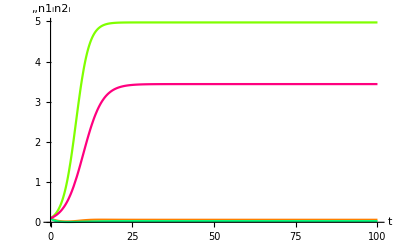

{n1_1→4.9726,n2_1→0.062151,n1_2→0.0286527,n2_2→3.43868}

```mathematica
(* multi-species *)
sol=EcoSim[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->-0.2,Subscript[x[n1], 2]->0.3,Subscript[x[n2], 2]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.1},100,Verbose->True];
PlotDynamics[sol]
FinalSlice[sol]
```

## *EcoEq

### tp

```mathematica
SetModel[tp]
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.3},{Var[Subscript[x, 1]]->0}]
SolveEcoEq[{Subscript[x, 1]->-0.3},{Var[x]->0}]
SolveEcoEq[{Subscript[x, 1]->-0.3,Var[x]->0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

```mathematica
(* 2sp, combined traits and Gs *)
SolveEcoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Var[x]->0.1}]
NSolveEcoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Var[x]->0.1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→3.78754,n2_1→-8.04707,n1_2→0,n2_2→0},{n1_1→0.211219,n2_1→-8.00264,n1_2→0,n2_2→0},{n1_1→4.00124,n2_1→0.0497067,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-8.04707,n2_2→3.78754},{n1_1→0,n2_1→0,n1_2→-8.00264,n2_2→0.211219},{n1_1→0,n2_1→0,n1_2→0.0497067,n2_2→4.00124},{n1_1→0.0672292,n2_1→-8.06806,n1_2→-8.06806,n2_2→0.0672292},{n1_1→3.96777,n2_1→0.0330625,n1_2→0.0330625,n2_2→3.96777}}

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→0.211219,n2_1→-8.00264,n1_2→0,n2_2→0},{n1_1→3.78754,n2_1→-8.04707,n1_2→0,n2_2→0},{n1_1→4.00124,n2_1→0.0497067,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-8.04707,n2_2→3.78754},{n1_1→0,n2_1→0,n1_2→-8.00264,n2_2→0.211219},{n1_1→0,n2_1→0,n1_2→0.0497067,n2_2→4.00124},{n1_1→0.0672292,n2_1→-8.06806,n1_2→-8.06806,n2_2→0.0672292},{n1_1→3.96777,n2_1→0.0330625,n1_2→0.0330625,n2_2→3.96777}}

```mathematica
eq=SolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349}}

```mathematica
SelectValid[eq]
```

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
ExtantSpecies/@SelectValid[eq]
```

{{},{n_1},{n_2},{n_1,n_2}}

```mathematica
eq=SolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},{Var[x][n1]->0.1,Var[x][n2]->0.2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349}}

```mathematica
NSolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
eq=FindEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},{Subscript[n1, 1]->5,Subscript[n2, 1]->0.5,Subscript[n1, 2]->0.5,Subscript[n2, 2]->5}]
```

{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

```mathematica
EcoEigenvalues[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq]
```

{-0.527297,-0.500664,-0.151327,-0.124694}

```mathematica
eq=FindEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3,Subscript[n1, 1]->5,Subscript[n2, 1]->0.5,Subscript[n1, 2]->0.5,Subscript[n2, 2]->5,Var[x]->0.1}]
```

{n1_1→3.75726,n2_1→0.24938,n1_2→0.24938,n2_2→3.75726}

```mathematica
EcoEigenvalues[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,{Var[x]->0.1},Verbose->True]
```

EcoEigenvalues: Jacobian={{-0.376389,0.01,-0.375726,0},{0.01,-0.175602,0,-0.024938},{-0.024938,0,-0.175602,0.01},{0,-0.375726,0.01,-0.376389}}

{-0.429473,-0.400664,-0.151327,-0.122518}

## EcoEvoSim

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},{Subscript[Var[x][n1], 1]->0.01,Subscript[Var[x][n2], 1]->0.01},1000,Verbose->True];
FinalSlice[sol]
```

EcoEvoSim: eqns=

{n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-1.01-0.1 n1_1[t]-2 x[n1]_1[t]-(x[n1]_1[t])^2),n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1.01-0.1 n2_1[t]+2 x[n2]_1[t]-(x[n2]_1[t])^2),x[n1]_1'[t]==0.01 (-2-2 x[n1]_1[t])+(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t],x[n2]_1'[t]==0.01 (2-2 x[n2]_1[t])+(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]}

EcoEvoSim: ics=

{x[n1]_1[0]==-0.8,x[n2]_1[0]==0.8,n1_1[0]==0.1,n2_1[0]==0.2}

EcoEvoSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1}

EcoEvoSim: bdwhens=

{}

EcoEvoSim: discretevars=

{}

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

```mathematica
(* combine traits, pops, vars *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[Var[x][n1], 1]->0.01,Subscript[Var[x][n2], 1]->0.01},1000];
FinalSlice[sol]
```

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

```mathematica
(* no comp-dependent vars *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[Var[x], 1]->0.01},1000];
FinalSlice[sol]
```

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

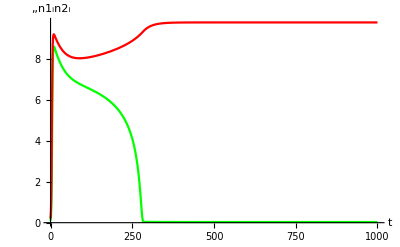

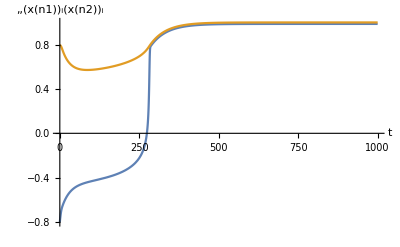

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

```mathematica
(* no species-dependent vars *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Var[x]->0.01},1000];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

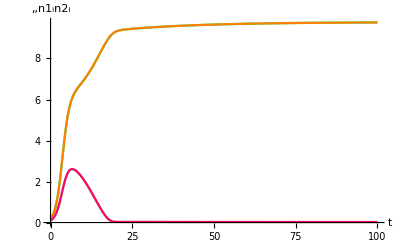

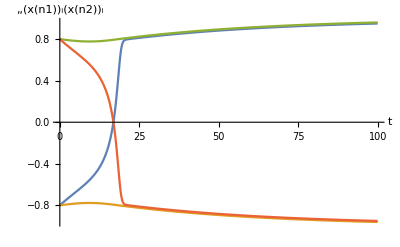

{n1_1→0.0256691,n2_1→9.7586,n1_2→9.7586,n2_2→0.0256691,x[n1]_1→0.950391,x[n2]_1→0.96086,x[n1]_2→-0.96086,x[n2]_2→-0.950391}

```mathematica
(* two species *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[x[n1], 2]->-0.8,Subscript[x[n2], 2]->0.8,Subscript[n1, 2]->0.2,Subscript[n2, 2]->0.1,Var[x]->0.01},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

```mathematica
(* just for exploration *)
d12=d21=0.01;sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Var[x]->0.01},1000,Verbose->False];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

-Graphics-

-Graphics-

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

## FindEcoEvoEq / *

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
eq=FindEcoEvoEq[{Subscript[n1, 1]->10,Subscript[n2, 1]->0.01,Subscript[n1, 2]->0.01,Subscript[n2, 2]->10,Subscript[x[n1], 1]->-1,Subscript[x[n2], 1]->-1,Subscript[x[n1], 2]->1,Subscript[x[n2], 2]->1},{Var[x]->0.2}]
```

{n1_1→7.87531,n2_1→0.0250076,n1_2→0.0250076,n2_2→7.87531,x[n1]_1→-0.999982,x[n2]_1→-0.774579,x[n1]_2→0.774579,x[n2]_2→0.999982}

```mathematica
EcoEvoEigenvalues[eq,{Var[x]->0.2},Verbose->False]
```

{-4.95157,-4.94896,-1.75456,-1.74945,-0.790032,-0.78231,-0.399974,-0.399974}

## EcoEvoVarSim

### tp

```mathematica
Clear[σμ]
```

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
σμ=0;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0},100,Verbose->True];
```

EcoEvoVarSim: eqns=

{n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-1-0.1 n1_1[t]-2 x[n1]_1[t]-(x[n1]_1[t])^2-(Var[x][n1])_1[t]),n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1-0.1 n2_1[t]+2 x[n2]_1[t]-(x[n2]_1[t])^2-(Var[x][n2])_1[t]),x[n1]_1'[t]==(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]+(-2-2 x[n1]_1[t]) (Var[x][n1])_1[t],x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]+(2-2 x[n2]_1[t]) (Var[x][n2])_1[t],(Var[x][n1])_1'[t]==-2 ((Var[x][n1])_1[t])^2+(0.01 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t],(Var[x][n2])_1'[t]==(0.01 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-2 ((Var[x][n2])_1[t])^2}

EcoEvoVarSim: ics=

{x[n1]_1[0]==-0.1,x[n2]_1[0]==0.2,n1_1[0]==0.1,n2_1[0]==0.1,(Var[x][n1])_1[0]==0,(Var[x][n2])_1[0]==0}

EcoEvoVarSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1,(Var[x][n1])_1,(Var[x][n2])_1}

EcoEvoVarSim: bdwhens=

{}

EcoEvoVarSim: discretevars=

{}

```mathematica
FinalSlice[sol]
```

{(Var[x][n1])_1→0.131421,(Var[x][n2])_1→0.131421,n1_1→8.63579,n2_1→8.63579,x[n1]_1→-0.929289,x[n2]_1→0.929289}

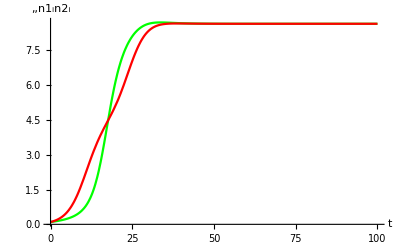

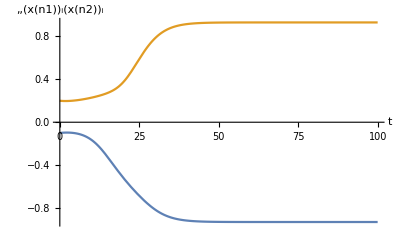

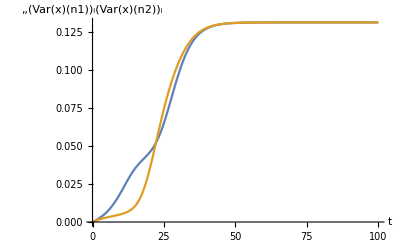

```mathematica
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
PlotDynamics[sol,{Var[x][n1],Var[x][n2]},PlotRange->{0,All}]
```

```mathematica
sol=EcoEvoVarSim[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0},100]
```

{(Var[x][n1])_1→InterpolatingFunction[…],(Var[x][n2])_1→InterpolatingFunction[…],n1_1→InterpolatingFunction[…],n2_1→InterpolatingFunction[…],x[n1]_1→InterpolatingFunction[…],x[n2]_1→InterpolatingFunction[…]}

```mathematica
d12=d21=10^-3;
sol=EcoEvoVarSim[
{Subscript[x[n1], 1]->-1,Subscript[x[n2], 1]->-1,Subscript[x[n1], 2]->1,Subscript[x[n2], 2]->1},
{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.1},
{Subscript[Var[x][n1], 1]->0.1,Subscript[Var[x][n2], 1]->0.1,Subscript[Var[x][n1], 2]->0.1,Subscript[Var[x][n2], 2]->0.1},
10^4];
```

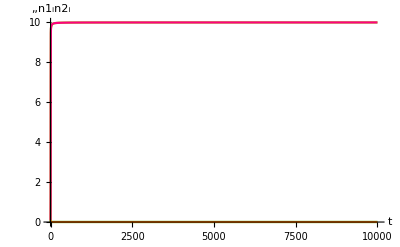

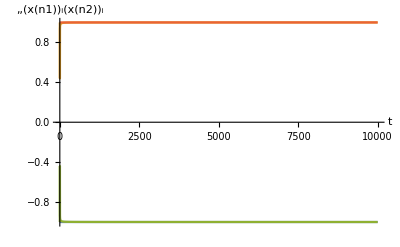

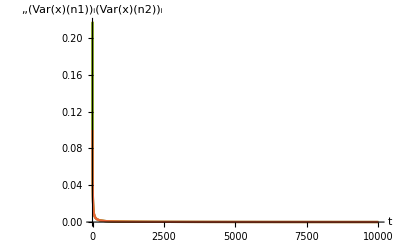

```mathematica
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
PlotDynamics[sol,{Var[x][n1],Var[x][n2]},PlotRange->{0,All}]
```

```mathematica
FinalSlice[sol]
```

{(Var[x][n1])_1→0.0000499835,(Var[x][n1])_2→0.000049986,(Var[x][n2])_1→0.000049986,(Var[x][n2])_2→0.0000499835,n1_1→9.98701,n2_1→0.00249688,n1_2→0.00249688,n2_2→9.98701,x[n1]_1→-1.,x[n2]_1→-0.99995,x[n1]_2→0.99995,x[n2]_2→1.}

```mathematica
d12=d21=0.01;
σμ=0.5;
sol=EcoEvoVarSim[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0},100,Verbose->True];
FinalSlice[sol]
```

EcoEvoVarSim: eqns=

{n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-1-0.1 n1_1[t]-2 x[n1]_1[t]-(x[n1]_1[t])^2-(Var[x][n1])_1[t]),n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1-0.1 n2_1[t]+2 x[n2]_1[t]-(x[n2]_1[t])^2-(Var[x][n2])_1[t]),x[n1]_1'[t]==(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]+(-2-2 x[n1]_1[t]) (Var[x][n1])_1[t],x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]+(2-2 x[n2]_1[t]) (Var[x][n2])_1[t],(Var[x][n1])_1'[t]==0.25-2 ((Var[x][n1])_1[t])^2+(0.01 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t],(Var[x][n2])_1'[t]==0.25+(0.01 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-2 ((Var[x][n2])_1[t])^2}

EcoEvoVarSim: ics=

{x[n1]_1[0]==-0.1,x[n2]_1[0]==0.2,n1_1[0]==0.1,n2_1[0]==0.1,(Var[x][n1])_1[0]==0,(Var[x][n2])_1[0]==0}

EcoEvoVarSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1,(Var[x][n1])_1,(Var[x][n2])_1}

EcoEvoVarSim: bdwhens=

{}

EcoEvoVarSim: discretevars=

{}

{(Var[x][n1])_1→0.379455,(Var[x][n2])_1→0.379455,n1_1→6.19886,n2_1→6.19886,x[n1]_1→-0.974323,x[n2]_1→0.974323}

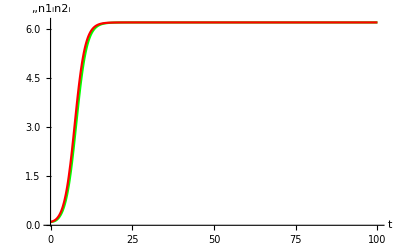

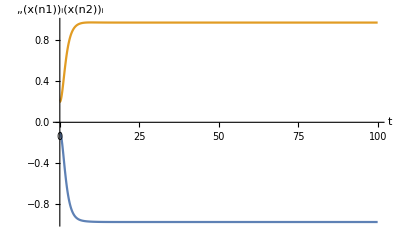

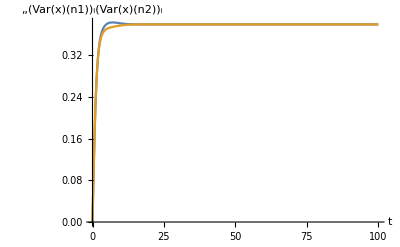

{(Var[x][n1])_1→0.379455,(Var[x][n2])_1→0.379455,n1_1→6.19886,n2_1→6.19886,x[n1]_1→-0.974323,x[n2]_1→0.974323}

```mathematica
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
PlotDynamics[sol,{Var[x][n1],Var[x][n2]},PlotRange->{0,All}]
FinalSlice[sol]
```

## FindEcoEvoVarEq / *

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
σμ=0;
```

```mathematica
(*debug=True;*)
eq=FindEcoEvoVarEq[{Subscript[Var[x][n1], 1]->0.1,Subscript[Var[x][n2], 1]->0.1,Subscript[n1, 1]->10,Subscript[n2, 1]->10,Subscript[x[n1], 1]->-0.9,Subscript[x[n2], 1]->0.9},Verbose->True]
(*debug=False;*)
```

FindEcoEvoVarEq: eqns=

{0==0.99 n1_1+0.01 n2_1+n1_1 (-1-0.1 n1_1-2 x[n1]_1-x[n1]_1^2-(Var[x][n1])_1),0==0.01 n1_1+0.99 n2_1+n2_1 (-1-0.1 n2_1+2 x[n2]_1-x[n2]_1^2-(Var[x][n2])_1),0==(0.01 n2_1 (-x[n1]_1+x[n2]_1))/n1_1+(-2-2 x[n1]_1) (Var[x][n1])_1,0==(0.01 n1_1 (x[n1]_1-x[n2]_1))/n2_1+(2-2 x[n2]_1) (Var[x][n2])_1,0==-2 (Var[x][n1])_1^2+(0.01 n2_1 ((-x[n1]_1+x[n2]_1)^2-(Var[x][n1])_1+(Var[x][n2])_1))/n1_1,0==(0.01 n1_1 ((x[n1]_1-x[n2]_1)^2+(Var[x][n1])_1-(Var[x][n2])_1))/n2_1-2 (Var[x][n2])_1^2}

FindEcoEvoVarEq: unksics=

{{n1_1,10},{n2_1,10},{x[n1]_1,-0.9},{x[n2]_1,0.9},{(Var[x][n1])_1,0.1},{(Var[x][n2])_1,0.1}}

{(Var[x][n1])_1→0.131421,(Var[x][n2])_1→0.131421,n1_1→8.63579,n2_1→8.63579,x[n1]_1→-0.929289,x[n2]_1→0.929289}

```mathematica
EcoEvoVarJacobian[eq]//MatrixForm
```

(-0.873579 | 0.01 | -1.22128 | 0 | -8.63579 | 0
0.01 | -0.873579 | 0 | 1.22128 | 0 | -8.63579
-0.00215218 | 0.00215218 | -0.272843 | 0.01 | -0.141421 | 0
-0.00215218 | 0.00215218 | 0.01 | -0.272843 | 0 | 0.141421
-0.004 | 0.004 | -0.0371716 | 0.0371716 | -0.535685 | 0.01
0.004 | -0.004 | -0.0371716 | 0.0371716 | 0.01 | -0.535685)

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-1.03518,-0.863579,-0.563188,-0.395115,-0.261814,-0.24534}

```mathematica
σμ=0.5;
eq=FindEcoEvoVarEq[{Subscript[Var[x][n1], 1]->0.1,Subscript[Var[x][n2], 1]->0.1,Subscript[n1, 1]->10,Subscript[n2, 1]->10,Subscript[x[n1], 1]->-0.9,Subscript[x[n2], 1]->0.9}]
EcoEvoVarEigenvalues[eq]
```

{(Var[x][n1])_1→0.379455,(Var[x][n2])_1→0.379455,n1_1→6.19886,n2_1→6.19886,x[n1]_1→-0.974323,x[n2]_1→0.974323}

{-1.61605,-1.5232,-0.773532,-0.766643,-0.619886,-0.553927}

## parameters / traits

```mathematica
RuleListSet[{zz->2}]
```

```mathematica
zz
```

2

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞
}]
```

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{δ,i,σ,ρ}
}]
```

```mathematica
δ=1;
```

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{0≤δ≤1,i≥0,σ≥0,ρ≥0}
}]
```

SetModel::badpar: One or more Parameters already defined. Clear them before running SetModel.

$Failed

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
```

{1,i,σ,ρ}

{δ,i,σ,ρ}

```mathematica
δ=.
```

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{0≤δ≤1,i≥0,σ≥0,ρ≥0}
}]
```

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
```

{δ,i,σ,ρ}

{δ,i,σ,ρ}

```mathematica
δ=1;
```

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
ParameterValues
```

{1,i,σ,ρ}

{δ,i,σ,ρ}

{δ→1,i→i,σ→σ,ρ→ρ}

```mathematica
ClearParameters
```

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
ParameterValues
```

{δ,i,σ,ρ}

{δ,i,σ,ρ}

{δ→δ,i→i,σ→σ,ρ→ρ}

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Traits->{-1≤x≤1}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{0≤δ≤1,i≥0,σ≥0,ρ≥0}
}]
```

```mathematica
EcoEvo`Private`range[x]
```

Interval[{-1,1}]

## adlv

```mathematica
GaussianIntegral[func_,{x_,mean_,var_}]:=Expectation[func,x\[Distributed]NormalDistribution[mean,Sqrt[var]]]
```

```mathematica
GaussianIntegralApprox[func_,{x_,mean_,var_}]:=(func+var/2 D[func,{x,2}])/.x->mean
```

```mathematica
GaussianIntegral[a[Subscript[x, i],x] Subscript[n, j],{x,Subscript[x, j],Subscript[Var[x], j]}]
```

Expectation[a[x_i,x] n_j,x\[Distributed]NormalDistribution[x_j,√(Var[x]_j)]]

```mathematica
GaussianIntegral[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],Subscript[x, j]]
```

```mathematica
GaussianIntegralApprox[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

a[x_i,x_j] n_j+1/2 n_j Var[x]_j a^(0,2)[x_i,x_j]

```mathematica
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
```

```mathematica
Simplify@GaussianIntegral[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2))

```mathematica
FullSimplify@GaussianIntegralApprox[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-x_j)^2/(2 σ^2)) n_j (2 σ^4-(σ+x_i-x_j) (σ-x_i+x_j) Var[x]_j))/(2 σ^4)

```mathematica
GaussianIntegral[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{Subscript[x, j],Subscript[x̄, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-(x̄)_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2))

```mathematica
Inactivate[{
{{Subscript[n, i]⇒∅},Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}] Subscript[n, i]},
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]}
},Sum]/.Inactive[Sum][stuff___,{ind_,𝒩[gu_]}]:>Sum[GaussianIntegral[(stuff/.Subscript[x, ind]->Subscript[unk[x], ind]),{Subscript[unk[x], ind],Subscript[x, ind],Subscript[Var[x], ind]}],{ind,𝒩[gu]},Method->"Procedural"]
```

{{{n_i⇒∅},n_i Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2)),{j,𝒩[n]},Method→Procedural]},{{0 n_i⇒n_i},r[x_i] n_i,NormalDistribution[0,σμ]}}

```mathematica
Inactivate[{
{{Subscript[n, i]⇒∅},Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}] Subscript[n, i]},
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]}
},Sum]/.Inactive[Sum][stuff___,{ind_,𝒩[gu_]}]:>Sum[GaussianIntegral[(stuff/.Subscript[x, ind]->Subscript[unk[x], ind]),{Subscript[unk[x], ind],Subscript[x, ind],Subscript[Var[x], ind]}]/.Subscript[unk[x], ind]->Subscript[x, ind],{ind,𝒩[gu]},Method->"Procedural"]
```

{{{n_i⇒∅},n_i Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2)),{j,𝒩[n]},Method→Procedural]},{{0 n_i⇒n_i},r[x_i] n_i,NormalDistribution[0,σμ]}}

```mathematica
Clear[a,r];
```

```mathematica
(* raw model *)
(*SetModel[{
Guild[n]->{Traits->{x}},
Transitions:>{
{{Subscript[n, i]⇒∅},Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}] Subscript[n, i]},
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]}
},
Parameters:>{σμ>=0,σ>=0}
}]*)
```

```mathematica
(* based on full gaussian integral *)
debug=True;
SetModel[{
Guild[n]->{Traits->{x}},
Transitions:>{
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]},
{{Subscript[n, i]⇒∅},Subscript[n, i] Sum[(ⅇ^(-(Subscript[x, i]-Subscript[x, j])^2/(2 (σ^2+Subscript[Var[x], j]))) Subscript[n, j])/(√(σ^2/(σ^2+Subscript[Var[x], j]))),{j,Subscript[𝒩, n]}]}
},
Parameters:>{σμ>=0,σ>=0}
}]
debug=False;
```

{sourcec,source,destc,dest}={0,n,1,n}

sourcetraits={x̲}

sourceG={{Var[x]_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={x̲}

destG={{Var[x]_i}}

fdest=r[x̲]

fdest′=r[x̲]+1/2 Var[x]_i r''[x̲]

dfdest′={r'[x̲]+1/2 Var[x]_i r^(3)[x̲]}

{sourcec,source,destc,dest}={1,n,1,∅}

sourcetraits={x̲}

sourceG={{Var[x]_i}}

fsource=-Sum[(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]

dfsource={-Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]}

d2fsource={{-Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j))+(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2),{j,𝒩[n]},Method→Procedural]}}

fsource′=-Sum[(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j))+(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2),{j,𝒩[n]},Method→Procedural]

dfsource′={-Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[(3 ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲)^3)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^3),{j,𝒩[n]},Method→Procedural]}

constructing dndt[n]...

constructing dxdt[n]...

constructing dGdt[n]...

```mathematica
(* see <https://mathematica.stackexchange.com/a/213105> by Bob Hanlon *)
sumRule=c1_. Sum[expr1_,iter_List,opts___]+c2_. Sum[expr2_,iter_List,opts___]:>Sum[c1 expr1+c2 expr2,iter,opts];
```

```mathematica
EcoEvo`Private`dndt[n]
```

n_i (-Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural])+n_i (r[x_i]+1/2 Var[x]_i r''[x_i])

```mathematica
Simplify[EcoEvo`Private`dndt[n]]
```

$Aborted

```mathematica
EcoEvo`Private`dndt[n]/.sumRule
```

n_i Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)))-1/2 Var[x]_i ((ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]+n_i (r[x_i]+1/2 Var[x]_i r''[x_i])

```mathematica
Simplify[EcoEvo`Private`dndt[n]/.sumRule]
```

n_i (r[x_i]+Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(σ √(1/(σ^2+Var[x]_j)))-1/2 Var[x]_i (-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j √(1/(σ^2+Var[x]_j)))/σ+(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2 (1/(σ^2+Var[x]_j))^(3/2))/σ),{j,𝒩[n]},Method→Procedural]+1/2 Var[x]_i r''[x_i])

```mathematica
EcoEvo`Private`dxdt[n]
```

{Var[x]_i (-Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^3)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^3)+(3 ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2),{j,𝒩[n]},Method→Procedural])+Var[x]_i (r'[x_i]+1/2 Var[x]_i r^(3)[x_i])}

```mathematica
EcoEvo`Private`dGdt[n]
```

{{-Var[x]_i^2 Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]+Var[x]_i^2 r''[x_i]+σμ^2 (r[x_i]+1/2 Var[x]_i r''[x_i])}}

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]
TraitEqns[{Subscript[𝒩, n]->1}]
VarEqns[{Subscript[𝒩, n]->1}]
```

{n_1'[t]==n_1[t] (-n_1[t]/(√(σ^2/(σ^2+Var[x]_1[t])))+(n_1[t] Var[x]_1[t])/(2 √(σ^2/(σ^2+Var[x]_1[t])) (σ^2+Var[x]_1[t])))+n_1[t] (r[x_1[t]]+1/2 Var[x]_1[t] r''[x_1[t]])}

{x_1'[t]==Var[x]_1[t] (r'[x_1[t]]+1/2 Var[x]_1[t] r^(3)[x_1[t]])}

{Var[x]_1'[t]==(n_1[t] (Var[x]_1[t])^2)/(√(σ^2/(σ^2+Var[x]_1[t])) (σ^2+Var[x]_1[t]))+(Var[x]_1[t])^2 r''[x_1[t]]+σμ^2 (r[x_1[t]]+1/2 Var[x]_1[t] r''[x_1[t]])}

```mathematica
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
r[x_]:=1-x^2;
```

```mathematica
p[xav_,σ_][x_]:=Evaluate@PDF[NormalDistribution[xav,σ]][x]
```

```mathematica
Assuming[σ>=0&&σi>=0&&σj>=0,Integrate[p[xi,σi][xi′]a[xi′,xj′]p[xj,σj][xj′],{xi′,-∞,∞},{xj′,-∞,∞}]]
```

(ⅇ^(-(xi-xj)^2/(2 (σ^2+σi^2+σj^2))) σ)/(√(σ^2+σi^2+σj^2))

```mathematica
ClearParameters
```

```mathematica
σ=10.0;
σμ=10^-2;
```

```mathematica
EcoEqns[{Subscript[x, 1]->0}]
```

{n_1'[t]==-1/2 n_1[t] (2 (-1+(0.1 n_1[t])/(√(1/(100.+Var[x]_1[t]))))+Var[x]_1[t] (2-0.1 n_1[t] √(1/(100.+Var[x]_1[t]))))}

```mathematica
EcoEqns[{Subscript[x, 1]->0}]
```

{n_1'[t]==n_1[t] (1-Var[x]_1[t])+n_1[t] (-(0.1 n_1[t])/(√(1/(100.+Var[x]_1[t])))-1/2 Var[x]_1[t] (-0.1 n_1[t] √(1/(100.+Var[x]_1[t]))+0. (1/(100.+Var[x]_1[t]))^(3/2)))}

```mathematica
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1},10,Verbose->True]
```

sol=NDSolve[{n_1'[t]==n_1[t]-1. n_1[t]^2,n_1[0]==0.1},{n_1},{t,0,10}]⟦1⟧

{n_1→InterpolatingFunction[…]}

```mathematica
TraitEqns[{Subscript[n, 1]->Subscript[n, 1]},{Subscript[Var[x], 1]->0.01}]
```

{x_1'[t]==0.-0.02 x_1[t]}

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->-0.9},{Subscript[n, 1]->0.1},{Subscript[Var[x], 1]->0.1},100,Verbose->True]
FinalSlice[sol]
```

EcoEvoSim: eqns=

{n_1'[t]==(-0.05 (0.-0.009995 n_1[t])-1.0005 n_1[t]) n_1[t]+n_1[t] (0.9-x_1[t]^2),x_1'[t]==0.-0.2 x_1[t]}

EcoEvoSim: ics=

{x_1[0]==-0.9,n_1[0]==0.1}

EcoEvoSim: unks=

{n_1,x_1}

EcoEvoSim: bdwhens=

{}

EcoEvoSim: discretevars=

{}

{n_1→InterpolatingFunction[…],x_1→InterpolatingFunction[…]}

{n_1→0.9,x_1→-9.42553×10^-10}

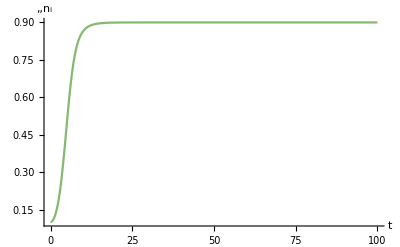

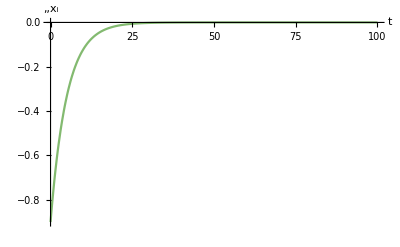

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

```mathematica
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9},{Subscript[n, 1]->0.1},{Subscript[Var[x], 1]->0},500,Verbose->True]
FinalSlice[sol]
```

EcoEvoVarSim: eqns=

{n_1'[t]==n_1[t] (1-x_1[t]^2-Var[x]_1[t])+n_1[t] (-(0.1 n_1[t])/(√(1/(100.+Var[x]_1[t])))-1/2 Var[x]_1[t] (-0.1 n_1[t] √(1/(100.+Var[x]_1[t]))+0. (1/(100.+Var[x]_1[t]))^(3/2))),x_1'[t]==-2 x_1[t] Var[x]_1[t]+Var[x]_1[t] (0. √(1/(100.+Var[x]_1[t]))-1/2 Var[x]_1[t] (0. (1/(100.+Var[x]_1[t]))^(3/2)+0. (1/(100.+Var[x]_1[t]))^(5/2))),Var[x]_1'[t]==(1-x_1[t]^2-Var[x]_1[t])/10000-2 (Var[x]_1[t])^2+0.1 n_1[t] (Var[x]_1[t])^2 √(1/(100.+Var[x]_1[t]))}

EcoEvoVarSim: ics=

{x_1[0]==-0.9,n_1[0]==0.1,Var[x]_1[0]==0}

EcoEvoVarSim: unks=

{n_1,x_1,Var[x]_1}

EcoEvoVarSim: bdwhens=

{}

EcoEvoVarSim: discretevars=

{}

{Var[x]_1→InterpolatingFunction[…],n_1→InterpolatingFunction[…],x_1→InterpolatingFunction[…]}

{Var[x]_1→0.00706259,n_1→0.992912,x_1→-0.00492873}

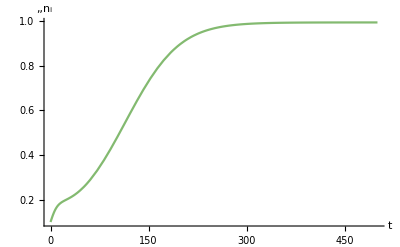

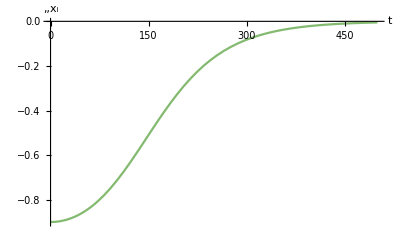

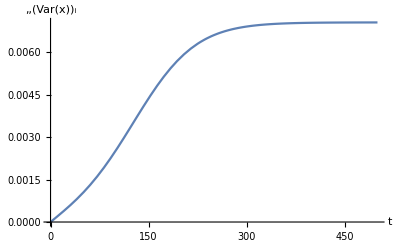

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

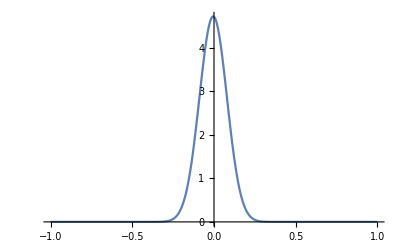

```mathematica
Plot[Evaluate[Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x]/.FinalSlice[sol]],{x,-1,1},PlotRange->All]
```

```mathematica
frames=Table[
Plot[Evaluate[Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x]/.Slice[sol,t]],{x,-1,1},PlotRange->{0,5},PlotLabel->t]
,{t,0,500,10}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

```mathematica
ListAnimate[frames]
```

```mathematica
σ=0.72;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.9},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},2000]
FinalSlice[sol]
```

{Var[x]_1→InterpolatingFunction[…],Var[x]_2→InterpolatingFunction[…],n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…],x_1→InterpolatingFunction[…],x_2→InterpolatingFunction[…]}

{Var[x]_1→0.0245486,Var[x]_2→0.0245486,n_1→0.487595,n_2→0.487595,x_1→-4.16735×10^-6,x_2→4.16735×10^-6}

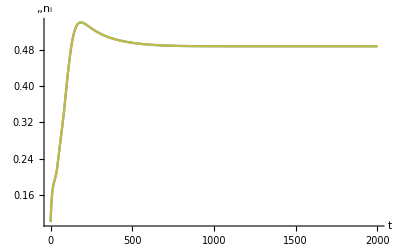

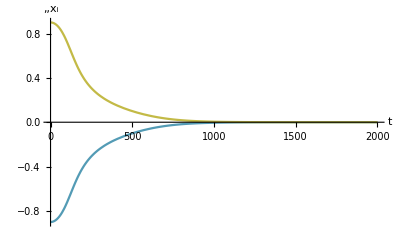

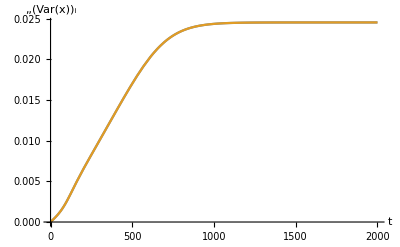

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

```mathematica
σ=0.65;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.9},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},2000];
FinalSlice[sol]
```

{Var[x]_1→0.0807618,Var[x]_2→0.0807618,n_1→0.457867,n_2→0.457867,x_1→7.19818×10^-11,x_2→-7.19818×10^-11}

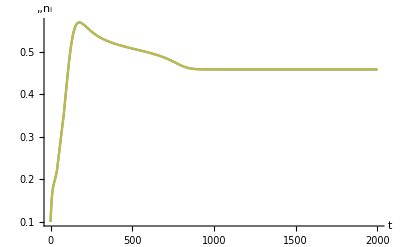

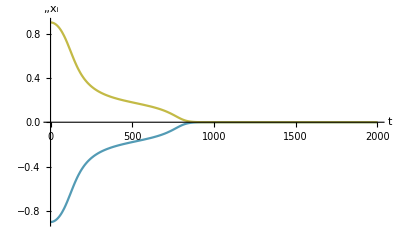

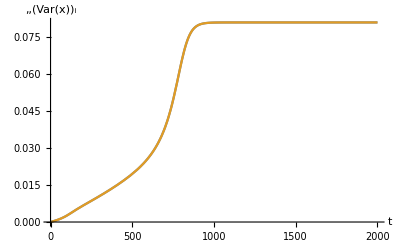

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

```mathematica
σ=0.4;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.89},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0.01,Subscript[Var[x], 2]->0.01},2000];
FinalSlice[sol]
```

{Var[x]_1→0.139689,Var[x]_2→0.347769,n_1→0.0161505,n_2→0.548879,x_1→9.20181×10^-12,x_2→5.84887×10^-13}

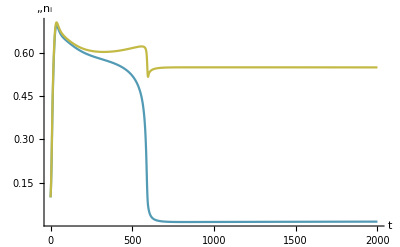

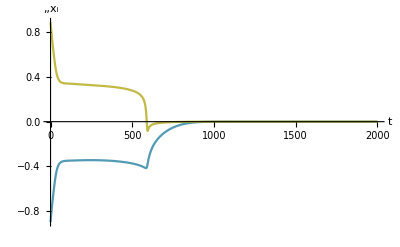

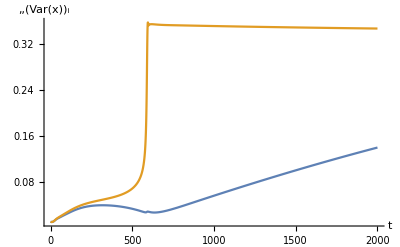

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

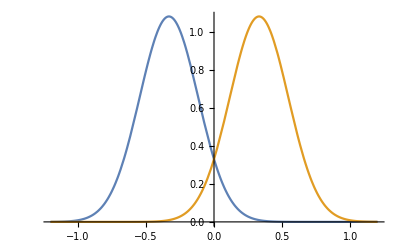

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
```

{Var[x]_1→0.0461595,Var[x]_2→0.0461595,n_1→0.582354,n_2→0.582354,x_1→-0.330853,x_2→0.330853}

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-0.854316,-0.383811,-0.132437,-0.0827446,-0.00824879,0.00710878}

```mathematica
eq=FindEcoEvoVarEq[{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5,Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Subscript[Var[x], 1]->0.05,Subscript[Var[x], 2]->0.05}]
```

{Var[x]_1→0.0581323,Var[x]_2→0.0581323,n_1→0.54924,n_2→0.54924,x_1→-0.314363,x_2→0.314363}

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-0.84646,-0.338634,-0.151261,-0.114782,0.0154427,0.0122013}

```mathematica
sol=EcoEvoVarSim[RuleListTweak[eq,Subscript[x, 1],0.01],20000];
FinalSlice[sol]
```

{Var[x]_1→0.340101,Var[x]_2→0.340072,n_1→0.427456,n_2→0.138121,x_1→3.34724×10^-28,x_2→1.74973×10^-27}

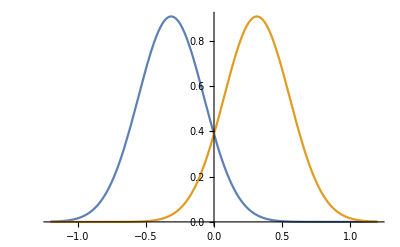

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
sol=EcoEvoVarSim[eq,1000];
FinalSlice[sol]
```

{Var[x]_1→0.0581323,Var[x]_2→0.0581323,n_1→0.54924,n_2→0.54924,x_1→-0.314363,x_2→0.314363}

```mathematica
σ=0.01;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.89},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0.01,Subscript[Var[x], 2]->0.01},200];
FinalSlice[sol]
```

{Var[x]_1→0.504129,Var[x]_2→0.495672,n_1→0.00714138,n_2→0.00699957,x_1→-3.6079×10^-22,x_2→-3.57031×10^-22}

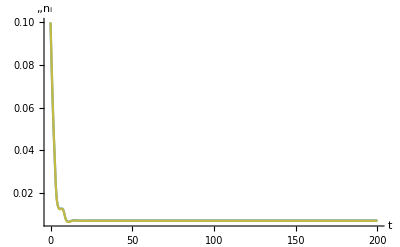

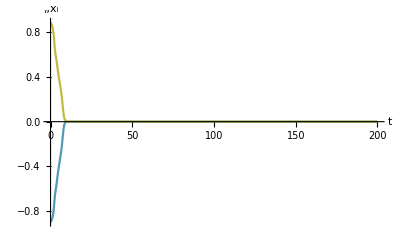

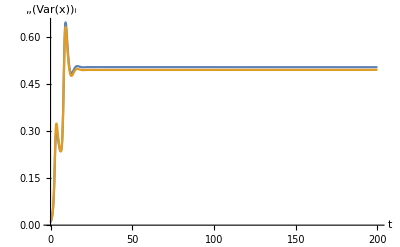

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

```mathematica
σμ=10^-4;
```

{Var[x]_1→0.000220335,Var[x]_2→0.000220335,n_1→0.529372,n_2→0.529372,x_1→-0.217868,x_2→0.217868}

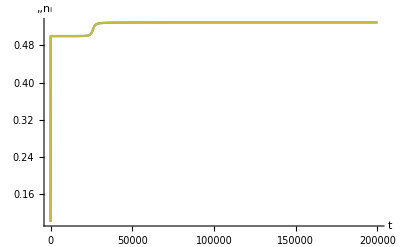

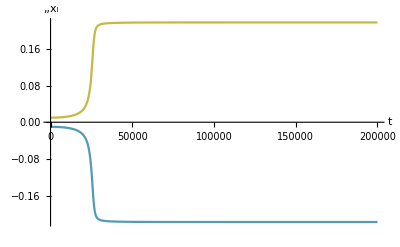

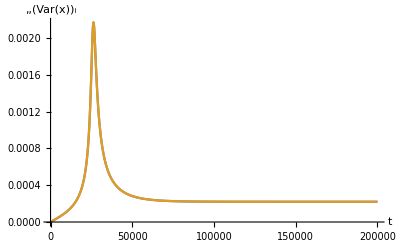

```mathematica
σ=0.65;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[x, 2]->0.01},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},200000];
FinalSlice[sol]
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

General::munfl: Exp[-2188.68] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4561.72] is too small to represent as a normalized machine number; precision may be lost.

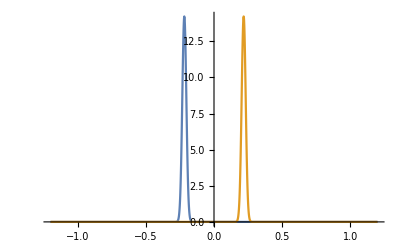

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

{Var[x]_1→0.250002,n_1→0.707104,x_1→-6.04351×10^-36}

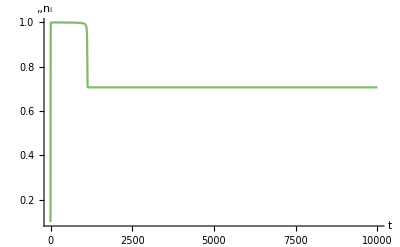

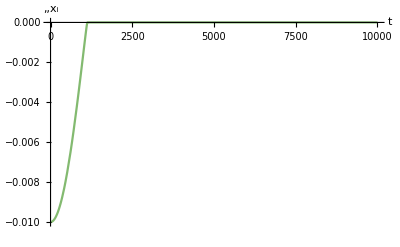

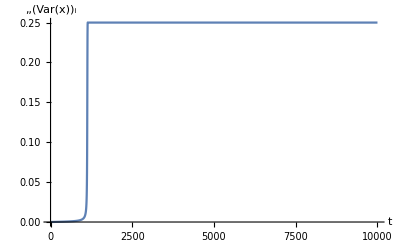

```mathematica
σμ=10^-3;
σ=0.5;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[n, 1]->0.1,Subscript[Var[x], 1]->0},10000];
FinalSlice[sol]
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

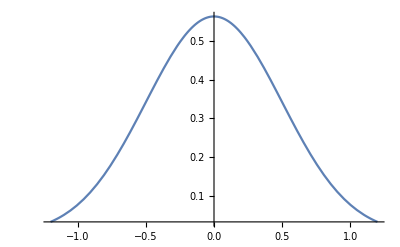

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

{Var[x]_1→0.00164603,Var[x]_2→0.00164603,n_1→0.629711,n_2→0.629711,x_1→-0.339619,x_2→0.339619}

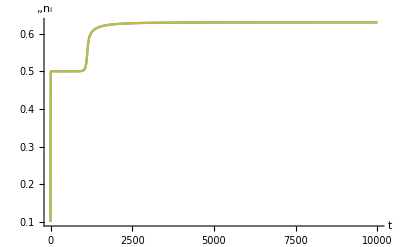

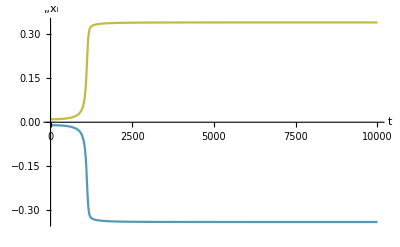

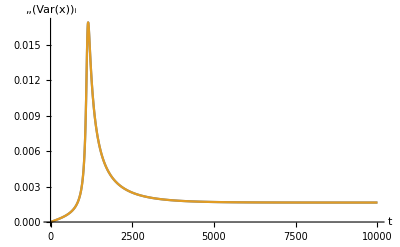

```mathematica
σμ=10^-3;
σ=0.5;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[x, 2]->0.01},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},10000];
FinalSlice[sol]
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

General::munfl: Exp[-720.] is too small to represent as a normalized machine number; precision may be lost.

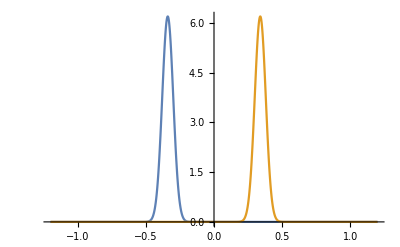

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
EcoEvoVarEigenvalues[eq]
```

{Var[x]_1→0.00164581,Var[x]_2→0.00164581,n_1→0.629711,n_2→0.629711,x_1→-0.33962,x_2→0.33962}

{-0.883863,-0.378441,-0.00514567,-0.00147206,-0.00107074,-0.000899443}

{Var[x]_1→0.00329039,Var[x]_2→0.00329039,n_1→0.625715,n_2→0.625715,x_1→-0.338193,x_2→0.338193}

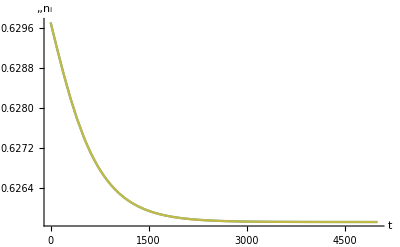

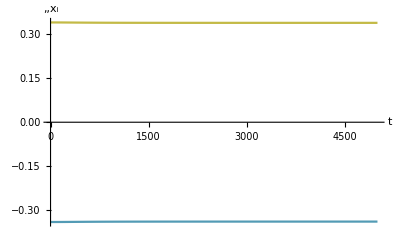

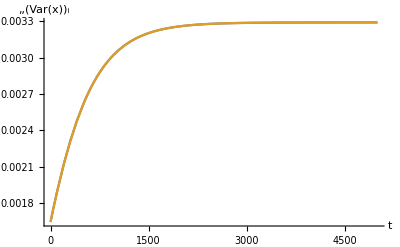

```mathematica
σμ=2 10^-3;
σ=0.5;
sol2=EcoEvoVarSim[eq,5000];
FinalSlice[sol2]
PlotDynamics[sol2,n]
PlotDynamics[sol2,x]
PlotDynamics[sol2,{Var[x]},PlotRange->{0,All}]
```

```mathematica
eq2=FindEcoEvoVarEq[FinalSlice[sol2]]
EcoEvoVarEigenvalues[eq2]
```

{Var[x]_1→0.00329045,Var[x]_2→0.00329045,n_1→0.625715,n_2→0.625715,x_1→-0.338193,x_2→0.338193}

{-0.884002,-0.373225,-0.0100714,-0.00314844,-0.00213072,-0.00159531}

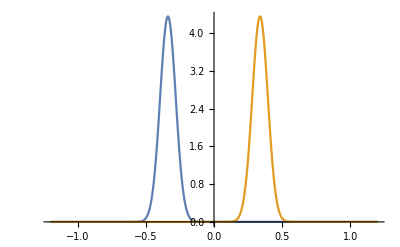

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq2],{x,-1.2,1.2},PlotRange->All]
```

{Var[x]_1→0.250009,Var[x]_2→0.250009,n_1→0.353548,n_2→0.353548,x_1→4.66616×10^-31,x_2→-4.44723×10^-31}

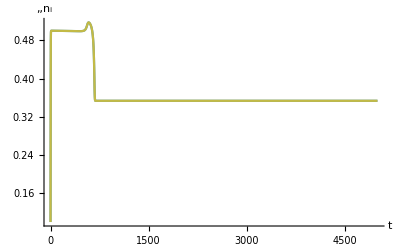

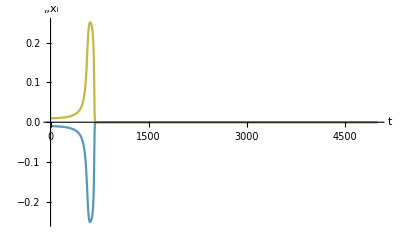

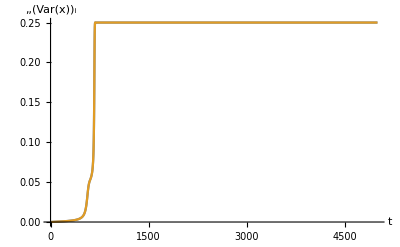

```mathematica
sol2′=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[x, 2]->0.01},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},5000];
FinalSlice[sol2′]
PlotDynamics[sol2′,n]
PlotDynamics[sol2′,x]
PlotDynamics[sol2′,{Var[x]},PlotRange->{0,All}]
```

```mathematica
eq2′=FindEcoEvoVarEq[FinalSlice[sol2′]]
EcoEvoVarEigenvalues[eq2′]
```

{Var[x]_1→0.250009,Var[x]_2→0.250009,n_1→0.0606926,n_2→0.646404,x_1→0,x_2→0}

{-0.437511+0.242103 ⅈ,-0.437511-0.242103 ⅈ,-0.500018,-0.375023,-0.0000279988,0}

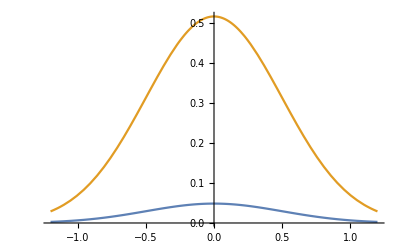

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq2′],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
eq2′′=FindEcoEvoVarEq[{Subscript[Var[x], 1]->0.05,Subscript[Var[x], 2]->0.05,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5,Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2}]
```

{Var[x]_1→0.0485673,Var[x]_2→0.0485673,n_1→0.522991,n_2→0.522991,x_1→-0.263463,x_2→0.263463}

```mathematica
EcoEvoVarEigenvalues[eq2′′]
```

{-0.886219,-0.249807,-0.0922321,-0.0499537,0.0248703,0.0180186}

{Var[x]_1→0.0171147,Var[x]_2→0.0171147,n_1→0.592876,n_2→0.592876,x_1→-0.323467,x_2→0.323467}

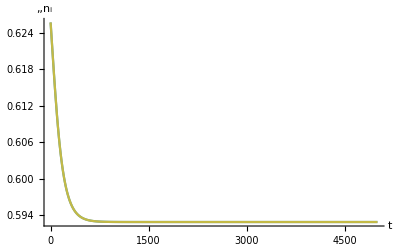

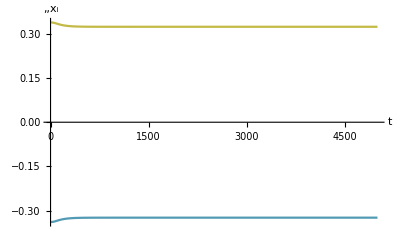

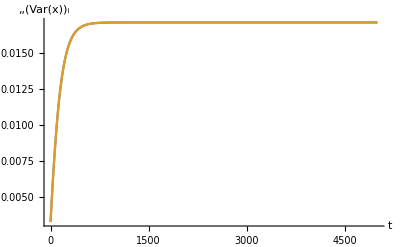

```mathematica
σμ=10^-2;
σ=0.5;
sol3=EcoEvoVarSim[eq2,5000];
FinalSlice[sol3]
PlotDynamics[sol3,n]
PlotDynamics[sol3,x]
PlotDynamics[sol3,{Var[x]},PlotRange->{0,All}]
```

```mathematica
eq3=FindEcoEvoVarEq[FinalSlice[sol3]]
EcoEvoVarEigenvalues[eq3]
```

{Var[x]_1→0.0171147,Var[x]_2→0.0171147,n_1→0.592876,n_2→0.592876,x_1→-0.323467,x_2→0.323467}

{-0.885254,-0.331873,-0.0444413,-0.0205705,-0.0085935,-0.00317141}

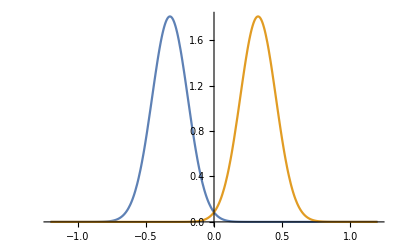

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq3],{x,-1.2,1.2},PlotRange->All]
```

{Var[x]_1→0.0291096,Var[x]_2→0.0291096,n_1→0.565465,n_2→0.565465,x_1→-0.305928,x_2→0.305928}

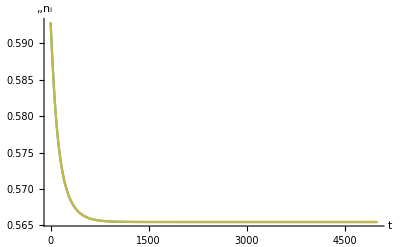

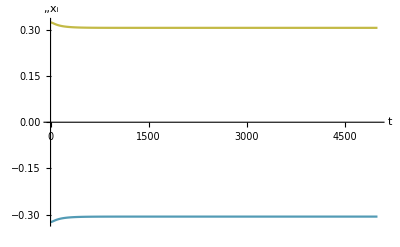

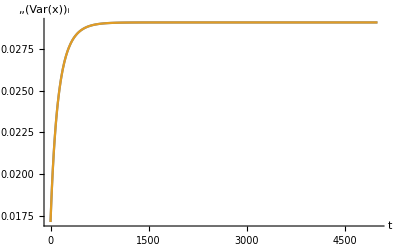

```mathematica
σμ=1.5 10^-2;
σ=0.5;
sol4=EcoEvoVarSim[eq3,5000];
FinalSlice[sol4]
PlotDynamics[sol4,n]
PlotDynamics[sol4,x]
PlotDynamics[sol4,{Var[x]},PlotRange->{0,All}]
```

```mathematica
eq4=FindEcoEvoVarEq[FinalSlice[sol4]]
EcoEvoVarEigenvalues[eq4]
```

{Var[x]_1→0.0291096,Var[x]_2→0.0291096,n_1→0.565465,n_2→0.565465,x_1→-0.305928,x_2→0.305928}

{-0.886078,-0.298989,-0.0672194,-0.0363211,-0.00594693,0.000442701}

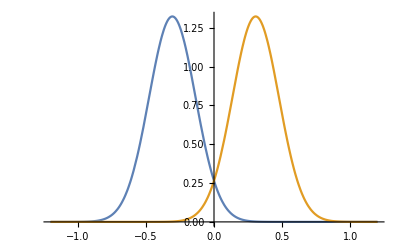

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq4],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
σμ=1.55 10^-2;
σ=0.5;
eq5=FindEcoEvoVarEq[eq4]
EcoEvoVarEigenvalues[eq5]
```

{Var[x]_1→0.031257,Var[x]_2→0.031257,n_1→0.560661,n_2→0.560661,x_1→-0.302212,x_2→0.302212}

{-0.886167,-0.293337,-0.0707912,-0.0388376,-0.00427534,0.00159107}

{Var[x]_1→0.251792,Var[x]_2→0.237011,n_1→0.647327,n_2→0.0591398,x_1→8.09881×10^-19,x_2→-1.39531×10^-15}

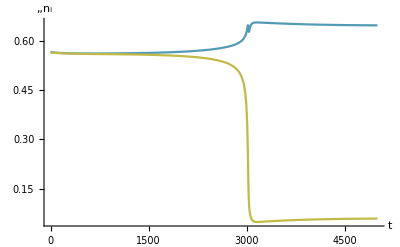

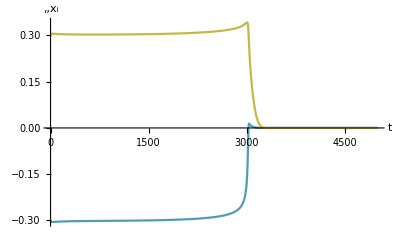

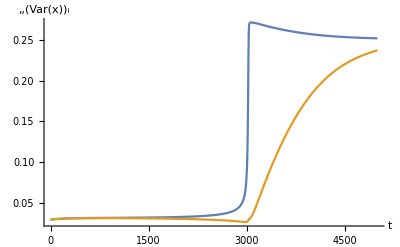

```mathematica
sol5=EcoEvoVarSim[RuleListTweak[eq4,Subscript[x, 1],0.001],5000];
FinalSlice[sol5]
PlotDynamics[sol5,n]
PlotDynamics[sol5,x]
PlotDynamics[sol5,{Var[x]},PlotRange->{0,All}]
```